# Motorbike net2 & net3

## Set Environment

```mathematica
home = "Y:/vault/pascal/";workdir = "C:/users/lichao/git/geonb/";
```

```mathematica
home = "Y:/vault/pami/next/single_airplane/";workdir = "C:/users/lichao/git/geonb/";
```

```mathematica
home = "Y:/vault/unsu/recheck/";workdir = "C:/users/lichao/git/geonb/";
```

```mathematica
SetDirectory[workdir];Needs["Posecpp`","posecpp_network.wl"];
```

```mathematica
prefix = "";suffix="";
```

## Generate Network 2

### load raw data

```mathematica
rawData=LoadNetwork2Raw[home<>prefix<>"net2_raw"<>suffix<>".txt"];rawData//Dimensions
```

{316845,8}

### find best threshold

```mathematica
Module[{n = 500,v=2,a},a =ConstructNetwork2[rawData,n,v];Sow[Length[a]];
Complement[a,ConstructNetwork2[rawData,n,v-0.1]]]//Reap;
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
VertexCount[g2]
EdgeCount[g2]
```

321

590

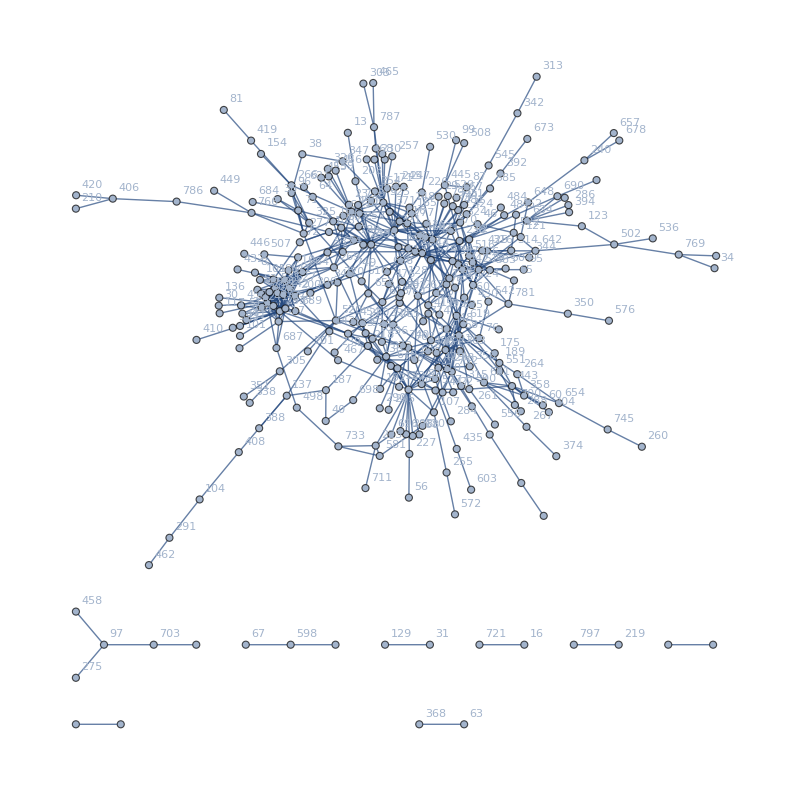

```mathematica
g2
```

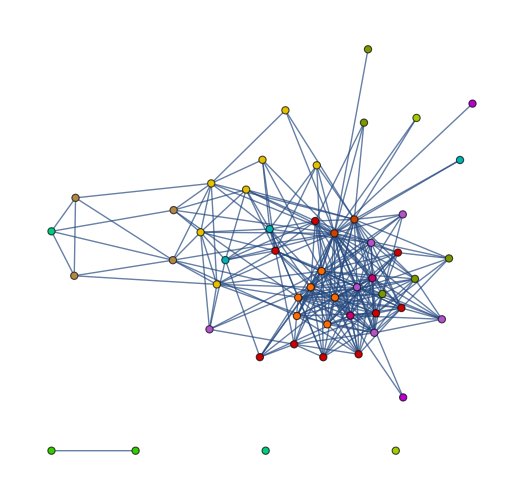

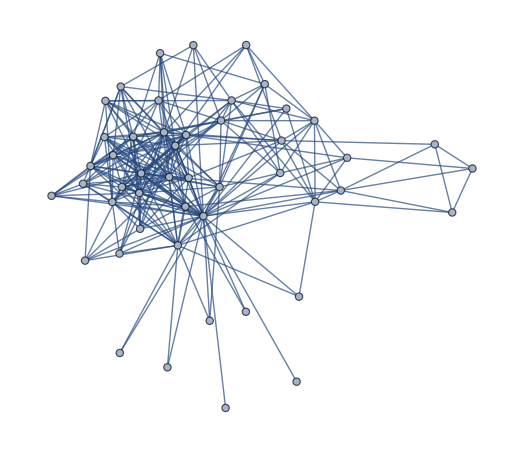

```mathematica
interGraph = Subgraph[g2,VertexList[g3]];
HighlightGraph[interGraph,comp3]
newg2= Subgraph[g2,ConnectedComponents[interGraph][[1]]]
```

```mathematica
VertexCount[newg2]
EdgeCount[newg2]
```

48

262

### Node Research

```mathematica
Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]]
```

{592,608,623,744,240,446,312,735,564,691,85,90,768,558,715,797,772,536,347,742,94,132,565,251,201,701,631,527,404,250,295,791,383,109,71,133,72,279,157,612,286,268,759,426,148,416,369,47,567,514,478,303,55,252,569,82,40,475,516,402,158,393,189,63,37,92,282,621,67,466,297,333,579,367,229,410,719,76,774,594,490,315,262,644,535,206,136,89,389,9,541,790,603,171,664,16,507,321,294,628,156,755,651,414,233,14,457,264,241,36,2,705,613,771,582,625,220,578,17,690,679,515,745,451,423,276,729,551,198,197,153,635,118,105,20,682,661,575,746,555,552,543,642,439,406,365,336,357,655,632,191,353,152,145,140,112,311,761,35,756,680,600,780,724,670,611,591,559,713,432,430,549,352,337,317,289,273,248,654,318,210,202,188,186,185,182,177,159,126,123,640,86,66,58,57,53,44,39,22}

```mathematica
HighlightGraph[NeighborhoodGraph[g2,271,VertexLabels->"Name"],VertexList[g3]]
```

### Export Graph

```mathematica
Export[home<>prefix<>"net2_el"<>suffix<>".txt",EdgeList[g2]]
```

Y:/vault/pascal/net2_el.txt

## Load Network 2

## Load Network 3

### read Edge List

```mathematica
el3=LoadNetwork3[home<>prefix<>"net3_el_02_02"<>suffix<>".txt"]
```

{36<->277,53<->92,54<->789,142<->477,200<->233,200<->780,233<->606,327<->566,340<->464,356<->707,358<->443,358<->700,359<->752,429<->587,429<->681,443<->587,443<->681,443<->707,447<->451,606<->641,631<->674,664<->674}

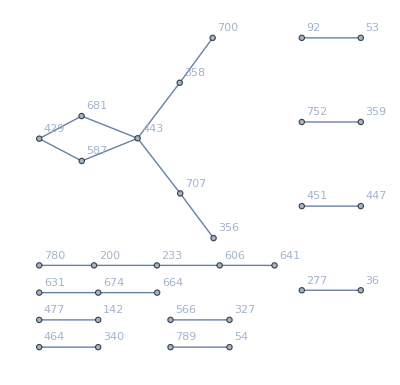

Set::write: Tag Inherited in Inherited["State"] is Protected.

```mathematica
g3=Graph[el3,VertexLabels->"Name"]
```

```mathematica
VertexList[g3]//Sort//Length
EdgeList[g3]//Length
```

88

71

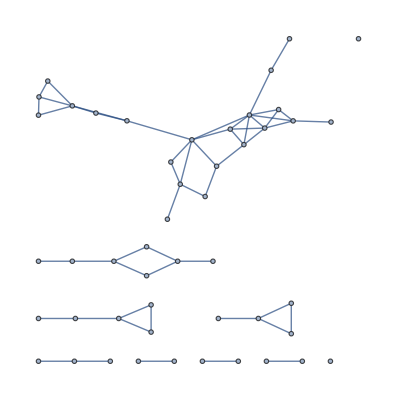

```mathematica
newg3=Subgraph[g3,newg2]
```

```mathematica
comp3=ConnectedComponents[Graph[el3]]
```

{{895,982,151,245,670,710,786,751,861,60,422,208,744,847,777,585,314,689,313,690,104,512,523,354,541,746,1004,517,637,771,783,787,798,844,693,954,841,451,496,785,902,130,418,615,811,968,890,709,362,100,804,969,538,923,338,248,503,561,613,162,227,207,913,921,794,887,724,178},{262,513,685,822,190,707,152,560,987,107,433,827,896,748,573,914,997,446,762},{29,10,137,263,228,348,453,653,93,352,520,35},{688,204,702,935,302,978,946,435,649,504,735,986},{320,117,458,128,624,629,635,98,74,264},{465,764,553,65,568,399,869,45,886},{889,3,161,965,938,960,518},{673,192,163,683},{57,223,554,53},{146,609,601},{604,643,888},{149,23,607},{225,25,555},{510,570,944},{701,605},{7,487},{368,188},{284,488},{115,389},{680,625},{46,145},{602,578},{577,729},{175,475},{580,200}}

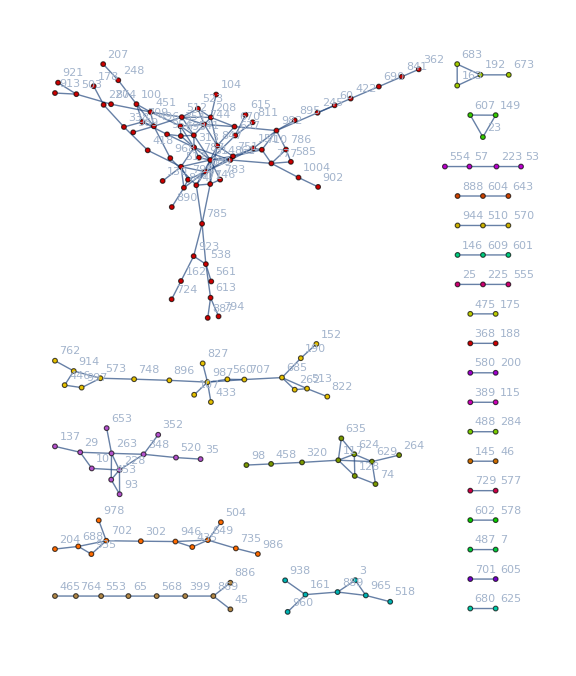

```mathematica
HighlightGraph[g3,comp3,ImageSize->Large]
```

```mathematica
Export[home<>prefix<>"net3_plot"<>suffix<>".pdf",%]
```

/home/lichao/scratch/pami/single_airplane/net3_plot_64.pdf

```mathematica
comp3=FindGraphCommunities[Graph[el3]]
```

{{151,861,104,208,613,746,884,118,162,785,923,637,670,751,847,314,512,523,541,744,313,354,787,947,689,771,783,798,489,538,887},{28,60,189,245,585,710,777,786,1004,422,446,914,982,997,690,688,935,702,895},{100,248,451,496,709,130,517,227,338,693,418,954,968,969,844,804,890},{223,387,605,726,261,404,735,302,946,649,919,435,701,543,839,828},{23,149,553,607,45,65,568,817,283,484,615,811},{161,294,888,938,960,291,465,764,869,583,604,886},{55,653,93,453,228,263,348,999,276,352,996},{3,889,965,225,555,518,741},{74,629,117,320,624,635,264},{91,235,316,284,488,815},{102,271,810,910,408},{556,696,872,1003},{200,580,822},{299,594,800},{439,625,680},{1,816},{39,51},{57,554},{68,961},{133,762},{147,643},{190,793},{192,673},{326,389},{362,841},{510,944},{557,559},{578,602},{601,609},{707,987},{806,922},{901,918}}

```mathematica
comp3=FindGraphCommunities[newg3]
```

{{105,268,626,736,612,501,304,744,763},{43,106,107,193,477,671,717},{79,311,72,95,239,485},{139,294,298,368,487,536},{382,546,742,630,591},{792,576,507,100},{160,187,140},{328,480},{555,728},{35,260},{16},{434}}

## Load Global data

```mathematica
{gx,gy,gs,gn}=LoadGlobalData[home<>prefix<>"converge_x"<>suffix<>".txt",home<>prefix<>"converge_y"<>suffix<>".txt",home<>prefix<>"converge_s"<>suffix<>".txt",home<>prefix<>"converge_n"<>suffix<>".txt"];
cx = gx+gs/2;cy=-(gy+gs/2);
```

```mathematica
cx;
```

```mathematica
Export[home<>prefix<>"global_summary"<>suffix<>".txt",Map[{#,gx[#],gy[#],gs[#]}&,Keys[gx]]]
```

Y:/vault/pami/next/single_airplane/global_summary.txt

```mathematica
Intersection[#,Keys[gx]]&/@comp3
```

{{31,58,59,245,292,559,638},{15,55,180,206,430,695},{7,43,120,374,722},{89,395,652},{33,62},{133,482},{136,333},{456,745},{641,733}}

```mathematica
Select[comp3,Length[#]>2&]
```

{{895,982,151,245,670,710,786,751,861,60,422,208,744,847,777,585,314,689,313,690,104,512,523,354,541,746,1004,517,637,771,783,787,798,844,693,954,841,451,496,785,902,130,418,615,811,968,890,709,362,100,804,969,538,923,338,248,503,561,613,162,227,207,913,921,794,887,724,178},{262,513,685,822,190,707,152,560,987,107,433,827,896,748,573,914,997,446,762},{29,10,137,263,228,348,453,653,93,352,520,35},{688,204,702,935,302,978,946,435,649,504,735,986},{320,117,458,128,624,629,635,98,74,264},{465,764,553,65,568,399,869,45,886},{889,3,161,965,938,960,518},{673,192,163,683},{57,223,554,53},{146,609,601},{604,643,888},{149,23,607},{225,25,555},{510,570,944}}

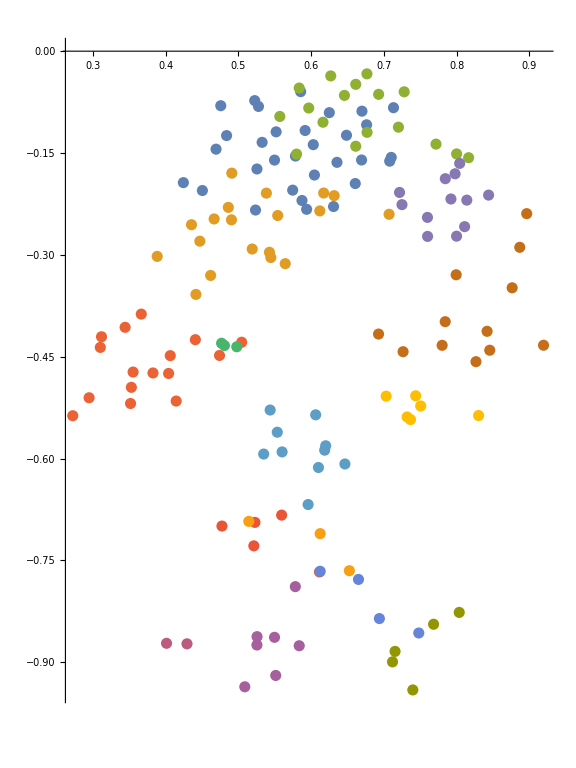

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,Select[comp3,Length[#]>2&],{2}],PlotRange->All,AspectRatio->4/3,ImageSize->Large]
```

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,comp3,{2}],PlotRange->All,AspectRatio->4/3]
```

```mathematica
Mean/@Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{0.360756,0.344439,0.362133,0.38136,0.352032,0.396469,0.767527,0.3965,0.372281,0.330848,0.836027,0.366872,0.475844,0.335979,0.410927,0.412599,0.766951,0.674244}

```mathematica
Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{{0.354006,0.361811,0.358521,0.341208,0.368141,0.380846},{0.330545,0.34774,0.342344,0.362643,0.338923},{0.374262,0.34284,0.363975,0.367456},{0.381039,0.389704,0.373338},{0.346285,0.357779},{0.39348,0.399458},{0.813928,0.721127},{0.38905,0.403949},{0.376815,0.367747},{0.334944,0.326751},{0.755648,0.916406},{0.370876,0.362867},{0.456433,0.495254},{0.333575,0.338383},{0.412666,0.409188},{0.407534,0.417664},{0.837074,0.696827},{0.785451,0.563036}}

```mathematica
sOrderByD = gs[#]&/@Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]];
```

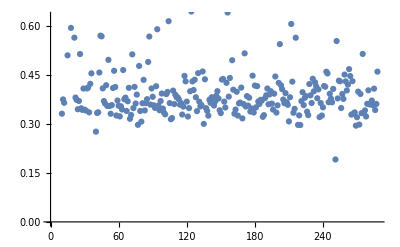

```mathematica
ListPlot[sOrderByD]
```

```mathematica
sOrderByP = gs[#]&/@Part[VertexList[g2],Ordering[PageRankCentrality[g2,0.1],All,Greater]];
```

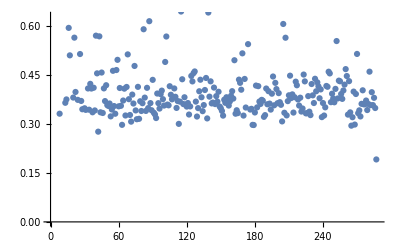

```mathematica
ListPlot[sOrderByP]
```

## Scale Slice

```mathematica
sLayers =SLayer[Keys[gx],gs]
```

<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Keys[gx]],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}]
```

{{93,119,211,242},{47,83,144,278,299},{130,148,376},{62,99},{292},{15,129},{238},{55,118}}

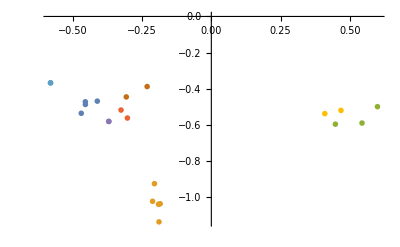

```mathematica
Module[{pos,idx},idx=DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}];pos=Map[{cx[#],cy[#]}&,idx,{2}];ListPlot[pos,PlotMarkers->idx]]
```

```mathematica
Export["ScaleLayer_"<>ToString[#]<>".pdf",SLayerPlot[#,sLayers,cx,cy]]&/@Keys[sLayers]
```

{ScaleLayer_6.pdf,ScaleLayer_5.pdf,ScaleLayer_4.pdf,ScaleLayer_3.pdf,ScaleLayer_8.pdf,ScaleLayer_9.pdf,ScaleLayer_7.pdf,ScaleLayer_1.pdf,ScaleLayer_10.pdf}

```mathematica
Directory
```

Directory

```mathematica
gall = Association[Map[#->{cx[#],cy[#],gs[#]}&,Keys[gx]]];
```

```mathematica
gall[0]
```

{0.111907,0.762903,0.476548}

```mathematica
SLayerPlot[1,sLayers,cx,cy]
```

SLayerPlot[1,<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>,cx,cy]

```mathematica
Manipulate[SLayerPlot[x,sLayers,cx,cy],{x,1,10,1}]
```

## Voronoi Centers for part

```mathematica
defined =Keys[gx];
```

```mathematica
voroComms= Intersection[defined,#]&/@Select[comp3,Length[#]>1&]
```

{{105,268,304,501,612,626,736,744,763},{43,106,107,193,477,671,717},{72,79,95,239,311,485},{139,294,298,368,487,536},{382,546,591,630,742},{100,507,576,792},{140,160,187},{328,480},{555,728},{35,260}}

```mathematica
centers =Mean/@Map[{gx[#],gy[#],Log[gs[#]]}&,voroComms,{2}]
```

{{-1.40882,-0.576347,-0.491948},{0.340279,-0.102082,-0.644462},{-1.55045,-0.321519,-0.538169},{-1.02274,-0.216805,-0.576281},{-1.20517,0.14597,-0.321124},{1.37332,-0.035153,-0.184234},{0.220983,0.120185,-0.790067},{-1.81625,-0.392541,0.120573},{-1.85442,-0.6238,-0.276838},{-0.958424,0.32075,-0.49529}}

```mathematica
ListPointPlot3D[centers]
```

-Graphics3D-

```mathematica
Length[centers]
```

10

```mathematica
Export[home<>prefix<>"voro_centers"<>suffix<>".txt",centers]
```

Y:/vault/pami/next/single_airplane/voro_centers.txt